# Largest product in a grid

In the 20×20 grid below, four numbers along a diagonal line have been marked in red.

The product of these numbers is 26 × 63 × 78 × 14 = 1788696.

What is the greatest product of four adjacent numbers in the same direction (up, down, left, right, or diagonally) in the 20×20 grid?

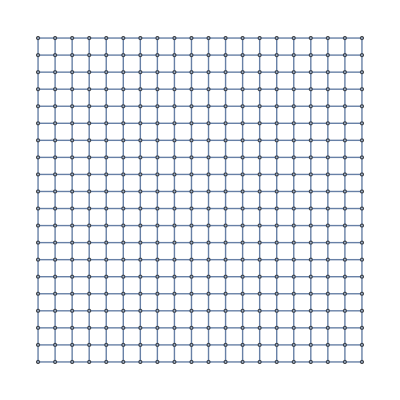

```mathematica
GridGraph[{20,20}]
```

```mathematica
SparseArray[Band[{1,1}]->{a,b,c,d,e}]
```

SparseArray[…]

```mathematica
Normal@SparseArray[Band[{1,1}]->{a,b,c,d,e}]
```

{{a,0,0,0,0},{0,b,0,0,0},{0,0,c,0,0},{0,0,0,d,0},{0,0,0,0,e}}

```mathematica
Normal@SparseArray[Band[{1,1}]->{a,b,c,d,e}]//MatrixForm
```

(a | 0 | 0 | 0 | 0
0 | b | 0 | 0 | 0
0 | 0 | c | 0 | 0
0 | 0 | 0 | d | 0
0 | 0 | 0 | 0 | e)

```mathematica
Normal@SparseArray[Band[{1,1},{5,5}]->{a,b,c,d,e}]//MatrixForm
```

(a | 0 | 0 | 0 | 0
0 | b | 0 | 0 | 0
0 | 0 | c | 0 | 0
0 | 0 | 0 | d | 0
0 | 0 | 0 | 0 | e)

```mathematica
Normal@SparseArray[Band[{1,1},{5,5},{1,0}]->{a,b,c,d,e}]//MatrixForm
```

(a | 0 | 0 | 0 | 0
b | 0 | 0 | 0 | 0
c | 0 | 0 | 0 | 0
d | 0 | 0 | 0 | 0
e | 0 | 0 | 0 | 0)

```mathematica
Normal@SparseArray[Band[{1,1},{5,5},{0,1}]->{a,b,c,d,e}]//MatrixForm
```

(a | b | c | d | e
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]]//MatrixForm
```

(1 | 1 | 1 | 1
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ArrayPad[Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]],{{0,10},{0,10}}]//Grid
```

1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Dimensions[ArrayPad[Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]],{{0,10},{0,10}}]]
```

{14,14}

```mathematica
ArrayPad[Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]],{{0,10-4},{0,10-4}}]//Grid
```

1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
ArrayPad[Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]],{{0,10-4},{0,10-4}}]//Grid
```

```mathematica
Dimensions[ArrayPad[Normal@SparseArray[Band[{1,1},{4,4},{0,1}]->ConstantArray[1,4]],{{0,10-4},{0,10-4}}]]
```

{10,10}

```mathematica
IntegerPartitions[10,{2}]
```

{{9,1},{8,2},{7,3},{6,4},{5,5}}

```mathematica
Dimensions[ArrayPad[Normal@SparseArray[Band[{2,2},{5,5},{0,1}]->ConstantArray[1,4]],{{0,10-5},{0,10-5}}]]
```

{10,10}

```mathematica
Dimensions@ArrayPad[Normal@SparseArray[Band[{1,1},{5,5},{0,1}]->ConstantArray[1,4]],{{0,10-5},{0,10-5}}]
```

{10,10}

```mathematica
ArrayPad[Normal@SparseArray[Band[{2,2},{5,5},{0,1}]->ConstantArray[1,4]],{{0,10-5},{0,10-5}}]//Grid
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
ArrayPad[Normal@SparseArray[Band[{2,1},{2,4},{0,1}]->ConstantArray[1,4]],{{0,10-5},{0,10-5}}]//Grid
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Dimensions[ArrayPad[Normal@SparseArray[Band[{2,1},{2,4},{0,1}]->ConstantArray[1,4]],{{0,10-5},{0,10-5}}]]
```

{7,9}

```mathematica
ImportString["08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"]
```

Import::fmterr: Cannot import data as BYU format.

$Failed

```mathematica
InputForm@"08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"
```

"08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08\n49 49 99 40 17 81 18 57 60 \
87 17 40 98 43 69 48 04 56 62 00\n81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 \
36 65\n52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91\n22 31 16 71 51 67 63 \
89 41 92 36 54 22 40 40 28 66 33 13 80\n24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 \
35 17 12 50\n32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70\n67 26 20 68 02 \
62 12 20 95 63 94 39 63 08 40 91 66 49 94 21\n24 55 58 05 66 73 99 26 97 17 78 78 96 83 \
14 88 34 89 63 72\n21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95\n78 17 53 \
28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92\n16 39 05 42 96 35 31 47 55 58 88 24 \
00 17 54 24 36 29 85 57\n86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58\n19 \
80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40\n04 52 08 83 97 35 99 16 07 97 \
57 32 16 26 26 79 33 27 98 66\n88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 \
69\n04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36\n20 69 36 41 72 30 23 88 \
34 62 99 69 82 67 59 85 74 04 36 16\n20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 \
57 05 54\n01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"

```mathematica
StringReplace["08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"," "->","]
```

08,02,22,97,38,15,00,40,00,75,04,05,07,78,52,12,50,77,91,08
49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,04,56,62,00
81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,03,49,13,36,65
52,70,95,23,04,60,11,42,69,24,68,56,01,32,56,71,37,02,36,91
22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80
24,47,32,60,99,03,45,02,44,75,33,53,78,36,84,20,35,17,12,50
32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70
67,26,20,68,02,62,12,20,95,63,94,39,63,08,40,91,66,49,94,21
24,55,58,05,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72
21,36,23,09,75,00,76,44,20,45,35,14,00,61,33,97,34,31,33,95
78,17,53,28,22,75,31,67,15,94,03,80,04,62,16,14,09,53,56,92
16,39,05,42,96,35,31,47,55,58,88,24,00,17,54,24,36,29,85,57
86,56,00,48,35,71,89,07,05,44,44,37,44,60,21,58,51,54,17,58
19,80,81,68,05,94,47,69,28,73,92,13,86,52,17,77,04,89,55,40
04,52,08,83,97,35,99,16,07,97,57,32,16,26,26,79,33,27,98,66
88,36,68,87,57,62,20,72,03,46,33,67,46,55,12,32,63,93,53,69
04,42,16,73,38,25,39,11,24,94,72,18,08,46,29,32,40,62,76,36
20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,04,36,16
20,73,35,29,78,31,90,01,74,31,49,71,48,86,81,16,23,57,05,54
01,70,54,71,83,51,54,69,16,92,33,48,61,43,52,01,89,19,67,48

```mathematica
grid=ImportString[StringReplace["08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48"," "->","]]
```

{{8,2,22,97,38,15,0,40,0,75,4,5,7,78,52,12,50,77,91,8},{49,49,99,40,17,81,18,57,60,87,17,40,98,43,69,48,4,56,62,0},{81,49,31,73,55,79,14,29,93,71,40,67,53,88,30,3,49,13,36,65},{52,70,95,23,4,60,11,42,69,24,68,56,1,32,56,71,37,2,36,91},{22,31,16,71,51,67,63,89,41,92,36,54,22,40,40,28,66,33,13,80},{24,47,32,60,99,3,45,2,44,75,33,53,78,36,84,20,35,17,12,50},{32,98,81,28,64,23,67,10,26,38,40,67,59,54,70,66,18,38,64,70},{67,26,20,68,2,62,12,20,95,63,94,39,63,8,40,91,66,49,94,21},{24,55,58,5,66,73,99,26,97,17,78,78,96,83,14,88,34,89,63,72},{21,36,23,9,75,0,76,44,20,45,35,14,0,61,33,97,34,31,33,95},{78,17,53,28,22,75,31,67,15,94,3,80,4,62,16,14,9,53,56,92},{16,39,5,42,96,35,31,47,55,58,88,24,0,17,54,24,36,29,85,57},{86,56,0,48,35,71,89,7,5,44,44,37,44,60,21,58,51,54,17,58},{19,80,81,68,5,94,47,69,28,73,92,13,86,52,17,77,4,89,55,40},{4,52,8,83,97,35,99,16,7,97,57,32,16,26,26,79,33,27,98,66},{88,36,68,87,57,62,20,72,3,46,33,67,46,55,12,32,63,93,53,69},{4,42,16,73,38,25,39,11,24,94,72,18,8,46,29,32,40,62,76,36},{20,69,36,41,72,30,23,88,34,62,99,69,82,67,59,85,74,4,36,16},{20,73,35,29,78,31,90,1,74,31,49,71,48,86,81,16,23,57,5,54},{1,70,54,71,83,51,54,69,16,92,33,48,61,43,52,1,89,19,67,48}}

```mathematica
Grid[grid]
```

8 | 2 | 22 | 97 | 38 | 15 | 0 | 40 | 0 | 75 | 4 | 5 | 7 | 78 | 52 | 12 | 50 | 77 | 91 | 8
49 | 49 | 99 | 40 | 17 | 81 | 18 | 57 | 60 | 87 | 17 | 40 | 98 | 43 | 69 | 48 | 4 | 56 | 62 | 0
81 | 49 | 31 | 73 | 55 | 79 | 14 | 29 | 93 | 71 | 40 | 67 | 53 | 88 | 30 | 3 | 49 | 13 | 36 | 65
52 | 70 | 95 | 23 | 4 | 60 | 11 | 42 | 69 | 24 | 68 | 56 | 1 | 32 | 56 | 71 | 37 | 2 | 36 | 91
22 | 31 | 16 | 71 | 51 | 67 | 63 | 89 | 41 | 92 | 36 | 54 | 22 | 40 | 40 | 28 | 66 | 33 | 13 | 80
24 | 47 | 32 | 60 | 99 | 3 | 45 | 2 | 44 | 75 | 33 | 53 | 78 | 36 | 84 | 20 | 35 | 17 | 12 | 50
32 | 98 | 81 | 28 | 64 | 23 | 67 | 10 | 26 | 38 | 40 | 67 | 59 | 54 | 70 | 66 | 18 | 38 | 64 | 70
67 | 26 | 20 | 68 | 2 | 62 | 12 | 20 | 95 | 63 | 94 | 39 | 63 | 8 | 40 | 91 | 66 | 49 | 94 | 21
24 | 55 | 58 | 5 | 66 | 73 | 99 | 26 | 97 | 17 | 78 | 78 | 96 | 83 | 14 | 88 | 34 | 89 | 63 | 72
21 | 36 | 23 | 9 | 75 | 0 | 76 | 44 | 20 | 45 | 35 | 14 | 0 | 61 | 33 | 97 | 34 | 31 | 33 | 95
78 | 17 | 53 | 28 | 22 | 75 | 31 | 67 | 15 | 94 | 3 | 80 | 4 | 62 | 16 | 14 | 9 | 53 | 56 | 92
16 | 39 | 5 | 42 | 96 | 35 | 31 | 47 | 55 | 58 | 88 | 24 | 0 | 17 | 54 | 24 | 36 | 29 | 85 | 57
86 | 56 | 0 | 48 | 35 | 71 | 89 | 7 | 5 | 44 | 44 | 37 | 44 | 60 | 21 | 58 | 51 | 54 | 17 | 58
19 | 80 | 81 | 68 | 5 | 94 | 47 | 69 | 28 | 73 | 92 | 13 | 86 | 52 | 17 | 77 | 4 | 89 | 55 | 40
4 | 52 | 8 | 83 | 97 | 35 | 99 | 16 | 7 | 97 | 57 | 32 | 16 | 26 | 26 | 79 | 33 | 27 | 98 | 66
88 | 36 | 68 | 87 | 57 | 62 | 20 | 72 | 3 | 46 | 33 | 67 | 46 | 55 | 12 | 32 | 63 | 93 | 53 | 69
4 | 42 | 16 | 73 | 38 | 25 | 39 | 11 | 24 | 94 | 72 | 18 | 8 | 46 | 29 | 32 | 40 | 62 | 76 | 36
20 | 69 | 36 | 41 | 72 | 30 | 23 | 88 | 34 | 62 | 99 | 69 | 82 | 67 | 59 | 85 | 74 | 4 | 36 | 16
20 | 73 | 35 | 29 | 78 | 31 | 90 | 1 | 74 | 31 | 49 | 71 | 48 | 86 | 81 | 16 | 23 | 57 | 5 | 54
1 | 70 | 54 | 71 | 83 | 51 | 54 | 69 | 16 | 92 | 33 | 48 | 61 | 43 | 52 | 1 | 89 | 19 | 67 | 48

```mathematica
SymbolicIndexedArray[u,{20,20}]//Grid
```

u11 | u12 | u13 | u14 | u15 | u16 | u17 | u18 | u19 | u110 | u111 | u112 | u113 | u114 | u115 | u116 | u117 | u118 | u119 | u120
u21 | u22 | u23 | u24 | u25 | u26 | u27 | u28 | u29 | u210 | u211 | u212 | u213 | u214 | u215 | u216 | u217 | u218 | u219 | u220
u31 | u32 | u33 | u34 | u35 | u36 | u37 | u38 | u39 | u310 | u311 | u312 | u313 | u314 | u315 | u316 | u317 | u318 | u319 | u320
u41 | u42 | u43 | u44 | u45 | u46 | u47 | u48 | u49 | u410 | u411 | u412 | u413 | u414 | u415 | u416 | u417 | u418 | u419 | u420
u51 | u52 | u53 | u54 | u55 | u56 | u57 | u58 | u59 | u510 | u511 | u512 | u513 | u514 | u515 | u516 | u517 | u518 | u519 | u520
u61 | u62 | u63 | u64 | u65 | u66 | u67 | u68 | u69 | u610 | u611 | u612 | u613 | u614 | u615 | u616 | u617 | u618 | u619 | u620
u71 | u72 | u73 | u74 | u75 | u76 | u77 | u78 | u79 | u710 | u711 | u712 | u713 | u714 | u715 | u716 | u717 | u718 | u719 | u720
u81 | u82 | u83 | u84 | u85 | u86 | u87 | u88 | u89 | u810 | u811 | u812 | u813 | u814 | u815 | u816 | u817 | u818 | u819 | u820
u91 | u92 | u93 | u94 | u95 | u96 | u97 | u98 | u99 | u910 | u911 | u912 | u913 | u914 | u915 | u916 | u917 | u918 | u919 | u920
u101 | u102 | u103 | u104 | u105 | u106 | u107 | u108 | u109 | u1010 | u1011 | u1012 | u1013 | u1014 | u1015 | u1016 | u1017 | u1018 | u1019 | u1020
u111 | u112 | u113 | u114 | u115 | u116 | u117 | u118 | u119 | u1110 | u1111 | u1112 | u1113 | u1114 | u1115 | u1116 | u1117 | u1118 | u1119 | u1120
u121 | u122 | u123 | u124 | u125 | u126 | u127 | u128 | u129 | u1210 | u1211 | u1212 | u1213 | u1214 | u1215 | u1216 | u1217 | u1218 | u1219 | u1220
u131 | u132 | u133 | u134 | u135 | u136 | u137 | u138 | u139 | u1310 | u1311 | u1312 | u1313 | u1314 | u1315 | u1316 | u1317 | u1318 | u1319 | u1320
u141 | u142 | u143 | u144 | u145 | u146 | u147 | u148 | u149 | u1410 | u1411 | u1412 | u1413 | u1414 | u1415 | u1416 | u1417 | u1418 | u1419 | u1420
u151 | u152 | u153 | u154 | u155 | u156 | u157 | u158 | u159 | u1510 | u1511 | u1512 | u1513 | u1514 | u1515 | u1516 | u1517 | u1518 | u1519 | u1520
u161 | u162 | u163 | u164 | u165 | u166 | u167 | u168 | u169 | u1610 | u1611 | u1612 | u1613 | u1614 | u1615 | u1616 | u1617 | u1618 | u1619 | u1620
u171 | u172 | u173 | u174 | u175 | u176 | u177 | u178 | u179 | u1710 | u1711 | u1712 | u1713 | u1714 | u1715 | u1716 | u1717 | u1718 | u1719 | u1720
u181 | u182 | u183 | u184 | u185 | u186 | u187 | u188 | u189 | u1810 | u1811 | u1812 | u1813 | u1814 | u1815 | u1816 | u1817 | u1818 | u1819 | u1820
u191 | u192 | u193 | u194 | u195 | u196 | u197 | u198 | u199 | u1910 | u1911 | u1912 | u1913 | u1914 | u1915 | u1916 | u1917 | u1918 | u1919 | u1920
u201 | u202 | u203 | u204 | u205 | u206 | u207 | u208 | u209 | u2010 | u2011 | u2012 | u2013 | u2014 | u2015 | u2016 | u2017 | u2018 | u2019 | u2020

```mathematica
SymbolicIndexedArray[u,{20,20}][[All,5]][[1;;4]]
```

{u15,u25,u35,u45}

```mathematica
SymbolicIndexedArray[u,{20,20}][[All,5]][[2;;5]]
```

{u25,u35,u45,u55}

```mathematica
SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]
```

{u175,u185,u195,u205}

```mathematica
Table[SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}]
```

{{u15,u25,u35,u45},{u25,u35,u45,u55},{u35,u45,u55,u65},{u45,u55,u65,u75},{u55,u65,u75,u85},{u65,u75,u85,u95},{u75,u85,u95,u105},{u85,u95,u105,u115},{u95,u105,u115,u125},{u105,u115,u125,u135},{u115,u125,u135,u145},{u125,u135,u145,u155},{u135,u145,u155,u165},{u145,u155,u165,u175},{u155,u165,u175,u185},{u165,u175,u185,u195},{u175,u185,u195,u205}}

```mathematica
Table[SymbolicIndexedArray[u,{20,20}][[All,7]][[k-3;;k]],{k,4,20}]
```

{{u17,u27,u37,u47},{u27,u37,u47,u57},{u37,u47,u57,u67},{u47,u57,u67,u77},{u57,u67,u77,u87},{u67,u77,u87,u97},{u77,u87,u97,u107},{u87,u97,u107,u117},{u97,u107,u117,u127},{u107,u117,u127,u137},{u117,u127,u137,u147},{u127,u137,u147,u157},{u137,u147,u157,u167},{u147,u157,u167,u177},{u157,u167,u177,u187},{u167,u177,u187,u197},{u177,u187,u197,u207}}

```mathematica
Table[SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}]
```

{{{u11,u21,u31,u41},{u21,u31,u41,u51},{u31,u41,u51,u61},{u41,u51,u61,u71},{u51,u61,u71,u81},{u61,u71,u81,u91},{u71,u81,u91,u101},{u81,u91,u101,u111},{u91,u101,u111,u121},{u101,u111,u121,u131},{u111,u121,u131,u141},{u121,u131,u141,u151},{u131,u141,u151,u161},{u141,u151,u161,u171},{u151,u161,u171,u181},{u161,u171,u181,u191},{u171,u181,u191,u201}},{{u12,u22,u32,u42},{u22,u32,u42,u52},{u32,u42,u52,u62},{u42,u52,u62,u72},{u52,u62,u72,u82},{u62,u72,u82,u92},{u72,u82,u92,u102},{u82,u92,u102,u112},{u92,u102,u112,u122},{u102,u112,u122,u132},{u112,u122,u132,u142},{u122,u132,u142,u152},{u132,u142,u152,u162},{u142,u152,u162,u172},{u152,u162,u172,u182},{u162,u172,u182,u192},{u172,u182,u192,u202}},{{u13,u23,u33,u43},{u23,u33,u43,u53},{u33,u43,u53,u63},{u43,u53,u63,u73},{u53,u63,u73,u83},{u63,u73,u83,u93},{u73,u83,u93,u103},{u83,u93,u103,u113},{u93,u103,u113,u123},{u103,u113,u123,u133},{u113,u123,u133,u143},{u123,u133,u143,u153},{u133,u143,u153,u163},{u143,u153,u163,u173},{u153,u163,u173,u183},{u163,u173,u183,u193},{u173,u183,u193,u203}},{{u14,u24,u34,u44},{u24,u34,u44,u54},{u34,u44,u54,u64},{u44,u54,u64,u74},{u54,u64,u74,u84},{u64,u74,u84,u94},{u74,u84,u94,u104},{u84,u94,u104,u114},{u94,u104,u114,u124},{u104,u114,u124,u134},{u114,u124,u134,u144},{u124,u134,u144,u154},{u134,u144,u154,u164},{u144,u154,u164,u174},{u154,u164,u174,u184},{u164,u174,u184,u194},{u174,u184,u194,u204}},{{u15,u25,u35,u45},{u25,u35,u45,u55},{u35,u45,u55,u65},{u45,u55,u65,u75},{u55,u65,u75,u85},{u65,u75,u85,u95},{u75,u85,u95,u105},{u85,u95,u105,u115},{u95,u105,u115,u125},{u105,u115,u125,u135},{u115,u125,u135,u145},{u125,u135,u145,u155},{u135,u145,u155,u165},{u145,u155,u165,u175},{u155,u165,u175,u185},{u165,u175,u185,u195},{u175,u185,u195,u205}},{{u16,u26,u36,u46},{u26,u36,u46,u56},{u36,u46,u56,u66},{u46,u56,u66,u76},{u56,u66,u76,u86},{u66,u76,u86,u96},{u76,u86,u96,u106},{u86,u96,u106,u116},{u96,u106,u116,u126},{u106,u116,u126,u136},{u116,u126,u136,u146},{u126,u136,u146,u156},{u136,u146,u156,u166},{u146,u156,u166,u176},{u156,u166,u176,u186},{u166,u176,u186,u196},{u176,u186,u196,u206}},{{u17,u27,u37,u47},{u27,u37,u47,u57},{u37,u47,u57,u67},{u47,u57,u67,u77},{u57,u67,u77,u87},{u67,u77,u87,u97},{u77,u87,u97,u107},{u87,u97,u107,u117},{u97,u107,u117,u127},{u107,u117,u127,u137},{u117,u127,u137,u147},{u127,u137,u147,u157},{u137,u147,u157,u167},{u147,u157,u167,u177},{u157,u167,u177,u187},{u167,u177,u187,u197},{u177,u187,u197,u207}},{{u18,u28,u38,u48},{u28,u38,u48,u58},{u38,u48,u58,u68},{u48,u58,u68,u78},{u58,u68,u78,u88},{u68,u78,u88,u98},{u78,u88,u98,u108},{u88,u98,u108,u118},{u98,u108,u118,u128},{u108,u118,u128,u138},{u118,u128,u138,u148},{u128,u138,u148,u158},{u138,u148,u158,u168},{u148,u158,u168,u178},{u158,u168,u178,u188},{u168,u178,u188,u198},{u178,u188,u198,u208}},{{u19,u29,u39,u49},{u29,u39,u49,u59},{u39,u49,u59,u69},{u49,u59,u69,u79},{u59,u69,u79,u89},{u69,u79,u89,u99},{u79,u89,u99,u109},{u89,u99,u109,u119},{u99,u109,u119,u129},{u109,u119,u129,u139},{u119,u129,u139,u149},{u129,u139,u149,u159},{u139,u149,u159,u169},{u149,u159,u169,u179},{u159,u169,u179,u189},{u169,u179,u189,u199},{u179,u189,u199,u209}},{{u110,u210,u310,u410},{u210,u310,u410,u510},{u310,u410,u510,u610},{u410,u510,u610,u710},{u510,u610,u710,u810},{u610,u710,u810,u910},{u710,u810,u910,u1010},{u810,u910,u1010,u1110},{u910,u1010,u1110,u1210},{u1010,u1110,u1210,u1310},{u1110,u1210,u1310,u1410},{u1210,u1310,u1410,u1510},{u1310,u1410,u1510,u1610},{u1410,u1510,u1610,u1710},{u1510,u1610,u1710,u1810},{u1610,u1710,u1810,u1910},{u1710,u1810,u1910,u2010}},{{u111,u211,u311,u411},{u211,u311,u411,u511},{u311,u411,u511,u611},{u411,u511,u611,u711},{u511,u611,u711,u811},{u611,u711,u811,u911},{u711,u811,u911,u1011},{u811,u911,u1011,u1111},{u911,u1011,u1111,u1211},{u1011,u1111,u1211,u1311},{u1111,u1211,u1311,u1411},{u1211,u1311,u1411,u1511},{u1311,u1411,u1511,u1611},{u1411,u1511,u1611,u1711},{u1511,u1611,u1711,u1811},{u1611,u1711,u1811,u1911},{u1711,u1811,u1911,u2011}},{{u112,u212,u312,u412},{u212,u312,u412,u512},{u312,u412,u512,u612},{u412,u512,u612,u712},{u512,u612,u712,u812},{u612,u712,u812,u912},{u712,u812,u912,u1012},{u812,u912,u1012,u1112},{u912,u1012,u1112,u1212},{u1012,u1112,u1212,u1312},{u1112,u1212,u1312,u1412},{u1212,u1312,u1412,u1512},{u1312,u1412,u1512,u1612},{u1412,u1512,u1612,u1712},{u1512,u1612,u1712,u1812},{u1612,u1712,u1812,u1912},{u1712,u1812,u1912,u2012}},{{u113,u213,u313,u413},{u213,u313,u413,u513},{u313,u413,u513,u613},{u413,u513,u613,u713},{u513,u613,u713,u813},{u613,u713,u813,u913},{u713,u813,u913,u1013},{u813,u913,u1013,u1113},{u913,u1013,u1113,u1213},{u1013,u1113,u1213,u1313},{u1113,u1213,u1313,u1413},{u1213,u1313,u1413,u1513},{u1313,u1413,u1513,u1613},{u1413,u1513,u1613,u1713},{u1513,u1613,u1713,u1813},{u1613,u1713,u1813,u1913},{u1713,u1813,u1913,u2013}},{{u114,u214,u314,u414},{u214,u314,u414,u514},{u314,u414,u514,u614},{u414,u514,u614,u714},{u514,u614,u714,u814},{u614,u714,u814,u914},{u714,u814,u914,u1014},{u814,u914,u1014,u1114},{u914,u1014,u1114,u1214},{u1014,u1114,u1214,u1314},{u1114,u1214,u1314,u1414},{u1214,u1314,u1414,u1514},{u1314,u1414,u1514,u1614},{u1414,u1514,u1614,u1714},{u1514,u1614,u1714,u1814},{u1614,u1714,u1814,u1914},{u1714,u1814,u1914,u2014}},{{u115,u215,u315,u415},{u215,u315,u415,u515},{u315,u415,u515,u615},{u415,u515,u615,u715},{u515,u615,u715,u815},{u615,u715,u815,u915},{u715,u815,u915,u1015},{u815,u915,u1015,u1115},{u915,u1015,u1115,u1215},{u1015,u1115,u1215,u1315},{u1115,u1215,u1315,u1415},{u1215,u1315,u1415,u1515},{u1315,u1415,u1515,u1615},{u1415,u1515,u1615,u1715},{u1515,u1615,u1715,u1815},{u1615,u1715,u1815,u1915},{u1715,u1815,u1915,u2015}},{{u116,u216,u316,u416},{u216,u316,u416,u516},{u316,u416,u516,u616},{u416,u516,u616,u716},{u516,u616,u716,u816},{u616,u716,u816,u916},{u716,u816,u916,u1016},{u816,u916,u1016,u1116},{u916,u1016,u1116,u1216},{u1016,u1116,u1216,u1316},{u1116,u1216,u1316,u1416},{u1216,u1316,u1416,u1516},{u1316,u1416,u1516,u1616},{u1416,u1516,u1616,u1716},{u1516,u1616,u1716,u1816},{u1616,u1716,u1816,u1916},{u1716,u1816,u1916,u2016}},{{u117,u217,u317,u417},{u217,u317,u417,u517},{u317,u417,u517,u617},{u417,u517,u617,u717},{u517,u617,u717,u817},{u617,u717,u817,u917},{u717,u817,u917,u1017},{u817,u917,u1017,u1117},{u917,u1017,u1117,u1217},{u1017,u1117,u1217,u1317},{u1117,u1217,u1317,u1417},{u1217,u1317,u1417,u1517},{u1317,u1417,u1517,u1617},{u1417,u1517,u1617,u1717},{u1517,u1617,u1717,u1817},{u1617,u1717,u1817,u1917},{u1717,u1817,u1917,u2017}},{{u118,u218,u318,u418},{u218,u318,u418,u518},{u318,u418,u518,u618},{u418,u518,u618,u718},{u518,u618,u718,u818},{u618,u718,u818,u918},{u718,u818,u918,u1018},{u818,u918,u1018,u1118},{u918,u1018,u1118,u1218},{u1018,u1118,u1218,u1318},{u1118,u1218,u1318,u1418},{u1218,u1318,u1418,u1518},{u1318,u1418,u1518,u1618},{u1418,u1518,u1618,u1718},{u1518,u1618,u1718,u1818},{u1618,u1718,u1818,u1918},{u1718,u1818,u1918,u2018}},{{u119,u219,u319,u419},{u219,u319,u419,u519},{u319,u419,u519,u619},{u419,u519,u619,u719},{u519,u619,u719,u819},{u619,u719,u819,u919},{u719,u819,u919,u1019},{u819,u919,u1019,u1119},{u919,u1019,u1119,u1219},{u1019,u1119,u1219,u1319},{u1119,u1219,u1319,u1419},{u1219,u1319,u1419,u1519},{u1319,u1419,u1519,u1619},{u1419,u1519,u1619,u1719},{u1519,u1619,u1719,u1819},{u1619,u1719,u1819,u1919},{u1719,u1819,u1919,u2019}},{{u120,u220,u320,u420},{u220,u320,u420,u520},{u320,u420,u520,u620},{u420,u520,u620,u720},{u520,u620,u720,u820},{u620,u720,u820,u920},{u720,u820,u920,u1020},{u820,u920,u1020,u1120},{u920,u1020,u1120,u1220},{u1020,u1120,u1220,u1320},{u1120,u1220,u1320,u1420},{u1220,u1320,u1420,u1520},{u1320,u1420,u1520,u1620},{u1420,u1520,u1620,u1720},{u1520,u1620,u1720,u1820},{u1620,u1720,u1820,u1920},{u1720,u1820,u1920,u2020}}}

```mathematica
Position[SymbolicIndexedArray[u,{20,20}],First@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]]
```

{{17,5}}

```mathematica
Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]
```

{{{17,5}},{{18,5}},{{19,5}},{{20,5}}}

```mathematica
SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]
```

{u175,u185,u195,u205}

```mathematica
SymbolicIndexedArray[u,{20,20}][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]
```

{{u175},{u185},{u195},{u205}}

```mathematica
Flatten[SymbolicIndexedArray[u,{20,20}][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]]
```

{u175,u185,u195,u205}

```mathematica
SameQ[SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]],Flatten[SymbolicIndexedArray[u,{20,20}][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]]]
```

True

```mathematica
Flatten[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]]
```

{38,72,78,83}

```mathematica
Times@@(Flatten[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]]])
```

17712864

```mathematica
Times@@@Times@@(grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[17;;20]])
```

{17712864}

```mathematica
Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}]
```

{{{38},{17},{55},{4}},{{17},{55},{4},{51}},{{55},{4},{51},{99}},{{4},{51},{99},{64}},{{51},{99},{64},{2}},{{99},{64},{2},{66}},{{64},{2},{66},{75}},{{2},{66},{75},{22}},{{66},{75},{22},{96}},{{75},{22},{96},{35}},{{22},{96},{35},{5}},{{96},{35},{5},{97}},{{35},{5},{97},{57}},{{5},{97},{57},{38}},{{97},{57},{38},{72}},{{57},{38},{72},{78}},{{38},{72},{78},{83}}}

```mathematica
TakeLargestBy[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}],Times@@Flatten[#]&,1]
```

{{{38},{72},{78},{83}}}

```mathematica
AssociationMap[Times@@Flatten[#]&,Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}]]
```

<|{{38},{17},{55},{4}}→142120,{{17},{55},{4},{51}}→190740,{{55},{4},{51},{99}}→1110780,{{4},{51},{99},{64}}→1292544,{{51},{99},{64},{2}}→646272,{{99},{64},{2},{66}}→836352,{{64},{2},{66},{75}}→633600,{{2},{66},{75},{22}}→217800,{{66},{75},{22},{96}}→10454400,{{75},{22},{96},{35}}→5544000,{{22},{96},{35},{5}}→369600,{{96},{35},{5},{97}}→1629600,{{35},{5},{97},{57}}→967575,{{5},{97},{57},{38}}→1050510,{{97},{57},{38},{72}}→15127344,{{57},{38},{72},{78}}→12164256,{{38},{72},{78},{83}}→17712864|>

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}]]]
```

<|{{38},{72},{78},{83}}→17712864,{{97},{57},{38},{72}}→15127344,{{57},{38},{72},{78}}→12164256,{{66},{75},{22},{96}}→10454400,{{75},{22},{96},{35}}→5544000,{{96},{35},{5},{97}}→1629600,{{4},{51},{99},{64}}→1292544,{{55},{4},{51},{99}}→1110780,{{5},{97},{57},{38}}→1050510,{{35},{5},{97},{57}}→967575,{{99},{64},{2},{66}}→836352,{{51},{99},{64},{2}}→646272,{{64},{2},{66},{75}}→633600,{{22},{96},{35},{5}}→369600,{{2},{66},{75},{22}}→217800,{{17},{55},{4},{51}}→190740,{{38},{17},{55},{4}}→142120|>

The algorithm is working correctly.

```mathematica
TakeLargestBy[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],Times@@Flatten[#]&,1]
```

```mathematica
Dimensions[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}]]
```

{20,17,4,1}

```mathematica
Dimensions[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,5]][[k-3;;k]],{k,4,20}]]
```

{17,4,1}

```mathematica
Dimensions[Flatten[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1]]
```

{340,4,1}

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1]]]//Short
```

<|{{66},{91},{88},{97}}→51267216,«338»,{{23},{53},{5},{0}}→0|>

```mathematica
TakeLargestBy[Flatten[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1],Times@@Flatten[#]&,1]
```

{{{66},{91},{88},{97}}}

```mathematica
TakeLargestBy[Flatten[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[k-3;;k]][[All,j]],{j,20},{k,4,20}],1],Times@@Flatten[#]&,1]
```

{{{66},{91},{88},{97}}}

```mathematica
grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[2;;5]][[All,7]]
```

{{18},{14},{11},{63}}

I can transpose the matrix to get the horizontal parts.

```mathematica
TakeLargestBy[Flatten[Table[Transpose[grid][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[k-3;;k]][[All,j]],{j,20},{k,4,20}],1],Times@@Flatten[#]&,1]
```

{{{78},{78},{96},{83}}}

Check the function

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[Transpose[grid][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1]]]//Short
```

<|{{78},{78},{96},{83}}→48477312,«338»,{{97},{38},{15},{0}}→0|>

## Diagonals

Analyze the diagonals.

```mathematica
Normal@SparseArray[Band[{1,1}]->ConstantArray[1,4]]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
grid[[1;;4,1;;4]]
```

{{8,2,22,97},{49,49,99,40},{81,49,31,73},{52,70,95,23}}

```mathematica
grid[[1;;4,1;;4]]//Grid
```

8 | 2 | 22 | 97
49 | 49 | 99 | 40
81 | 49 | 31 | 73
52 | 70 | 95 | 23

```mathematica
Diagonal[grid[[1;;4,1;;4]]]
```

{8,49,31,23}

```mathematica
grid[[1;;4,2;;5]]//Grid
```

2 | 22 | 97 | 38
49 | 99 | 40 | 17
49 | 31 | 73 | 55
70 | 95 | 23 | 4

```mathematica
grid[[2;;5,1;;4]]//Grid
```

49 | 49 | 99 | 40
81 | 49 | 31 | 73
52 | 70 | 95 | 23
22 | 31 | 16 | 71

```mathematica
Flatten[Table[Diagonal[grid[[j-3;;j,k-3;;k]]],{j,4,20},{k,4,20}],1]
```

{{8,49,31,23},{2,99,73,4},{22,40,55,60},{97,17,79,11},{38,81,14,42},{15,18,29,69},{0,57,93,24},{40,60,71,68},{0,87,40,56},{75,17,67,1},{4,40,53,32},{5,98,88,56},{7,43,30,71},{78,69,3,37},{52,48,49,2},{12,4,13,36},{50,56,36,91},{49,49,95,71},{49,31,23,51},{99,73,4,67},{40,55,60,63},{17,79,11,89},{81,14,42,41},{18,29,69,92},{57,93,24,36},{60,71,68,54},{87,40,56,22},{17,67,1,40},{40,53,32,40},{98,88,56,28},{43,30,71,66},{69,3,37,33},{48,49,2,13},{4,13,36,80},{81,70,16,60},{49,95,71,99},{31,23,51,3},{73,4,67,45},{55,60,63,2},{79,11,89,44},{14,42,41,75},{29,69,92,33},{93,24,36,53},{71,68,54,78},{40,56,22,36},{67,1,40,84},{53,32,40,20},{88,56,28,35},{30,71,66,17},{3,37,33,12},{49,2,13,50},{52,31,32,28},{70,16,60,64},{95,71,99,23},{23,51,3,67},{4,67,45,10},{60,63,2,26},{11,89,44,38},{42,41,75,40},{69,92,33,67},{24,36,53,59},{68,54,78,54},{56,22,36,70},{1,40,84,66},{32,40,20,18},{56,28,35,38},{71,66,17,64},{37,33,12,70},{22,47,81,68},{31,32,28,2},{16,60,64,62},{71,99,23,12},{51,3,67,20},{67,45,10,95},{63,2,26,63},{89,44,38,94},{41,75,40,39},{92,33,67,63},{36,53,59,8},{54,78,54,40},{22,36,70,91},{40,84,66,66},{40,20,18,49},{28,35,38,94},{66,17,64,21},{24,98,20,5},{47,81,68,66},{32,28,2,73},{60,64,62,99},{99,23,12,26},{3,67,20,97},{45,10,95,17},{2,26,63,78},{44,38,94,78},{75,40,39,96},{33,67,63,83},{53,59,8,14},{78,54,40,88},{36,70,91,34},{84,66,66,89},{20,18,49,63},{35,38,94,72},{32,26,58,9},{98,20,5,75},{81,68,66,0},{28,2,73,76},{64,62,99,44},{23,12,26,20},{67,20,97,45},{10,95,17,35},{26,63,78,14},{38,94,78,0},{40,39,96,61},{67,63,83,33},{59,8,14,97},{54,40,88,34},{70,91,34,31},{66,66,89,33},{18,49,63,95},{67,55,23,28},{26,58,9,22},{20,5,75,75},{68,66,0,31},{2,73,76,67},{62,99,44,15},{12,26,20,94},{20,97,45,3},{95,17,35,80},{63,78,14,4},{94,78,0,62},{39,96,61,16},{63,83,33,14},{8,14,97,9},{40,88,34,53},{91,34,31,56},{66,89,33,92},{24,36,53,42},{55,23,28,96},{58,9,22,35},{5,75,75,31},{66,0,31,47},{73,76,67,55},{99,44,15,58},{26,20,94,88},{97,45,3,24},{17,35,80,0},{78,14,4,17},{78,0,62,54},{96,61,16,24},{83,33,14,36},{14,97,9,29},{88,34,53,85},{34,31,56,57},{21,17,5,48},{36,53,42,35},{23,28,96,71},{9,22,35,89},{75,75,31,7},{0,31,47,5},{76,67,55,44},{44,15,58,44},{20,94,88,37},{45,3,24,44},{35,80,0,60},{14,4,17,21},{0,62,54,58},{61,16,24,51},{33,14,36,54},{97,9,29,17},{34,53,85,58},{78,39,0,68},{17,5,48,5},{53,42,35,94},{28,96,71,47},{22,35,89,69},{75,31,7,28},{31,47,5,73},{67,55,44,92},{15,58,44,13},{94,88,37,86},{3,24,44,52},{80,0,60,17},{4,17,21,77},{62,54,58,4},{16,24,51,89},{14,36,54,55},{9,29,17,40},{16,56,81,83},{39,0,68,97},{5,48,5,35},{42,35,94,99},{96,71,47,16},{35,89,69,7},{31,7,28,97},{47,5,73,57},{55,44,92,32},{58,44,13,16},{88,37,86,26},{24,44,52,26},{0,60,17,79},{17,21,77,33},{54,58,4,27},{24,51,89,98},{36,54,55,66},{86,80,8,87},{56,81,83,57},{0,68,97,62},{48,5,35,20},{35,94,99,72},{71,47,16,3},{89,69,7,46},{7,28,97,33},{5,73,57,67},{44,92,32,46},{44,13,16,55},{37,86,26,12},{44,52,26,32},{60,17,79,63},{21,77,33,93},{58,4,27,53},{51,89,98,69},{19,52,68,73},{80,8,87,38},{81,83,57,25},{68,97,62,39},{5,35,20,11},{94,99,72,24},{47,16,3,94},{69,7,46,72},{28,97,33,18},{73,57,67,8},{92,32,46,46},{13,16,55,29},{86,26,12,32},{52,26,32,40},{17,79,63,62},{77,33,93,76},{4,27,53,36},{4,36,16,41},{52,68,73,72},{8,87,38,30},{83,57,25,23},{97,62,39,88},{35,20,11,34},{99,72,24,62},{16,3,94,99},{7,46,72,69},{97,33,18,82},{57,67,8,67},{32,46,46,59},{16,55,29,85},{26,12,32,74},{26,32,40,4},{79,63,62,36},{33,93,76,16},{88,42,36,29},{36,16,41,78},{68,73,72,31},{87,38,30,90},{57,25,23,1},{62,39,88,74},{20,11,34,31},{72,24,62,49},{3,94,99,71},{46,72,69,48},{33,18,82,86},{67,8,67,81},{46,46,59,16},{55,29,85,23},{12,32,74,57},{32,40,4,5},{63,62,36,54},{4,69,35,71},{42,36,29,83},{16,41,78,51},{73,72,31,54},{38,30,90,69},{25,23,1,16},{39,88,74,92},{11,34,31,33},{24,62,49,48},{94,99,71,61},{72,69,48,43},{18,82,86,52},{8,67,81,1},{46,59,16,89},{29,85,23,19},{32,74,57,67},{40,4,5,48}}

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[Diagonal[grid[[j-3;;j,k-3;;k]]],{j,4,20},{k,4,20}],1]]]//Short
```

<|{94,99,71,61}→40304286,«287»,{0,57,93,24}→0|>

## Compare the largest diagonal, row, and column

The largest vertical column:

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[grid[[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1]]]//Short
```

<|{{66},{91},{88},{97}}→51267216,«338»,{{23},{53},{5},{0}}→0|>

The largest horizontal row product:

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[Transpose[grid][[##]]&@@@Position[SymbolicIndexedArray[u,{20,20}],#]&/@SymbolicIndexedArray[u,{20,20}][[All,j]][[k-3;;k]],{j,20},{k,4,20}],1]]]//Short
```

<|{{78},{78},{96},{83}}→48477312,«338»,{{97},{38},{15},{0}}→0|>

The largest diagonal:

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[Diagonal[grid[[j-3;;j,k-3;;k]]],{j,4,20},{k,4,20}],1]]]//Short
```

<|{94,99,71,61}→40304286,«287»,{0,57,93,24}→0|>

We can see the column has the greatest product.

I forgot about the antidiagonal.

```mathematica
ResourceFunction["Antidiagonal"][({{a, b}, {c, d}})]
```

{b,c}

```mathematica
Reverse[Diagonal[Reverse[({{a, b}, {c, d}})]]]
```

{b,c}

```mathematica
Diagonal[Reverse[({{a, b}, {c, d}})]]
```

{c,b}

This is the same because we are only concerned about the product.

```mathematica
ReverseSort[AssociationMap[Times@@Flatten[#]&,Flatten[Table[Diagonal[Reverse[grid[[j-3;;j,k-3;;k]]]],{j,4,20},{k,4,20}],1]]]//Short
```

<|{87,97,94,89}→70600674,«287»,«1»→0|>